```mathematica
ClearAll["Global`*"]
```

```mathematica
amat=({{0, 1, 0, 0}, {-n^2 kR, 0, 0, -n(kR-1)}, {0, 0, 0, 1}, {0, n(kT-1), 4 n^2 kT, 0}});
eiga=FullSimplify[Eigenvalues[amat]]
```

{-(√(-((1+(-5+kR) kT) n^2)-√((1+2 (-5+9 kR) kT+(-5+kR)^2 kT^2) n^4)))/(√2),(√(-((1+(-5+kR) kT) n^2)-√((1+2 (-5+9 kR) kT+(-5+kR)^2 kT^2) n^4)))/(√2),-(√(-((1+(-5+kR) kT) n^2)+√((1+2 (-5+9 kR) kT+(-5+kR)^2 kT^2) n^4)))/(√2),(√(-((1+(-5+kR) kT) n^2)+√((1+2 (-5+9 kR) kT+(-5+kR)^2 kT^2) n^4)))/(√2)}

```mathematica
eiga/.{n->1}
eiga/.{n->1,kT->1}
eiga/.{n->1,kT->0}
eiga/.{n->1,kR->0}
eiga/.{n->1,kT->0,kR->0}
```

{-(√(-1-(-5+kR) kT-√(1+2 (-5+9 kR) kT+(-5+kR)^2 kT^2)))/(√2),(√(-1-(-5+kR) kT-√(1+2 (-5+9 kR) kT+(-5+kR)^2 kT^2)))/(√2),-(√(-1-(-5+kR) kT+√(1+2 (-5+9 kR) kT+(-5+kR)^2 kT^2)))/(√2),(√(-1-(-5+kR) kT+√(1+2 (-5+9 kR) kT+(-5+kR)^2 kT^2)))/(√2)}

{-(√(4-kR-√(1+(-5+kR)^2+2 (-5+9 kR))))/(√2),(√(4-kR-√(1+(-5+kR)^2+2 (-5+9 kR))))/(√2),-(√(4-kR+√(1+(-5+kR)^2+2 (-5+9 kR))))/(√2),(√(4-kR+√(1+(-5+kR)^2+2 (-5+9 kR))))/(√2)}

{-ⅈ,ⅈ,0,0}

{-(√(-1+5 kT-√(1-10 kT+25 kT^2)))/(√2),(√(-1+5 kT-√(1-10 kT+25 kT^2)))/(√2),-(√(-1+5 kT+√(1-10 kT+25 kT^2)))/(√2),(√(-1+5 kT+√(1-10 kT+25 kT^2)))/(√2)}

{-ⅈ,ⅈ,0,0}

```mathematica
kRex=Range[-1,1,0.1]
eiga[[1]]/.{n->1,kT->1,kR->kRex}
```

{-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

{-1.,-0.948683,-0.894427,-0.83666,-0.774597,-0.707107,-0.632456,-0.547723,-0.447214,-0.316228,0.,0.-0.316228 ⅈ,0.-0.447214 ⅈ,0.-0.547723 ⅈ,0.-0.632456 ⅈ,0.-0.707107 ⅈ,0.-0.774597 ⅈ,0.-0.83666 ⅈ,0.-0.894427 ⅈ,0.-0.948683 ⅈ,0.-1. ⅈ}

```mathematica
Manipulate[Show[
ListPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kT->kTman,kR->kRman}],Im[eiga[[k]]/.{n->1,kT->kTman,kR->kRman}]},{k,1,4}],
AxesLabel->{"Real","Imaginary"},PlotStyle->{Black,Thick}]
],
{kTman,-1,1},{kRman,-1,1}
]
```

```mathematica
Manipulate[Show[
{
ParametricPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kT->kTman}],Im[eiga[[k]]/.{n->1,kT->kTman}]},{k,1,4}],
{kR,-1,1},
AxesLabel->{"Real","Imaginary"}
],
ListPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kT->kTman,kR->kRman}],Im[eiga[[k]]/.{n->1,kT->kTman,kR->kRman}]},{k,1,4}],
AxesLabel->{"Real","Imaginary"},PlotStyle->{Black,PointSize[Large]}
]
}],
{kTman,-1,1},{kRman,-1,1}
]
```

```mathematica
Manipulate[Show[
{
ParametricPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kR->kRman}],Im[eiga[[k]]/.{n->1,kR->kRman}]},{k,1,4}],
{kT,-1,1},
AxesLabel->{"Real","Imaginary"}
],
ListPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kT->kTman,kR->kRman}],Im[eiga[[k]]/.{n->1,kT->kTman,kR->kRman}]},{k,1,4}],
AxesLabel->{"Real","Imaginary"},PlotStyle->{Black,PointSize[Large]}
]
}],
{kTman,-1,1},{kRman,-1,1}
]
```

```mathematica
Manipulate[Show[
ParametricPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kT->kTman}],Im[eiga[[k]]/.{n->1,kT->kTman}]},{k,1,4}],
{kR,-1,1},
AxesLabel->{"Real","Imaginary"}]
],
{kTman,-1,1}
]
```

```mathematica
Manipulate[Show[
ParametricPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kR->kRman}],Im[eiga[[k]]/.{n->1,kR->kRman}]},{k,1,4}],
{kT,-1,1},
AxesLabel->{"Real","Imaginary"}]
],{kRman,-1,1}
]
```

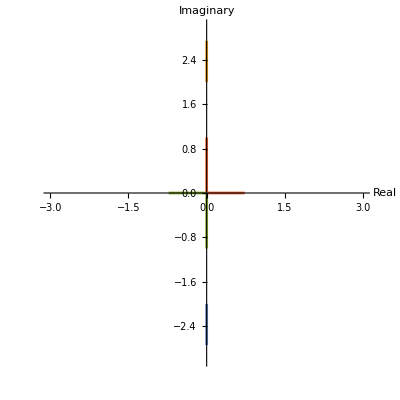
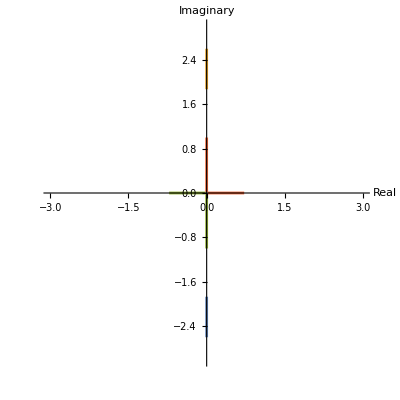
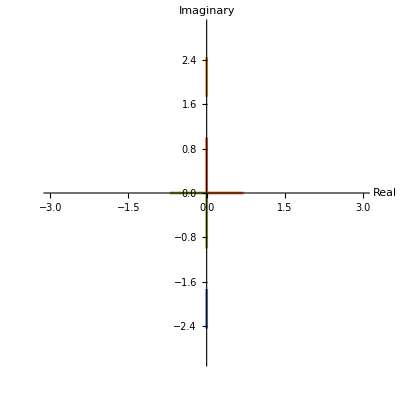
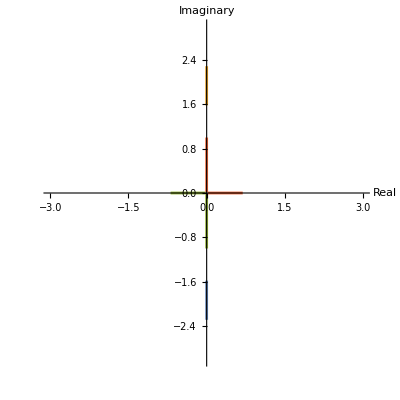
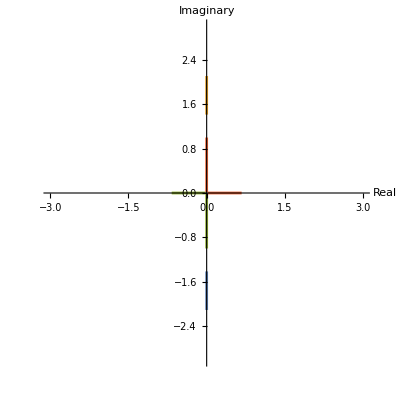
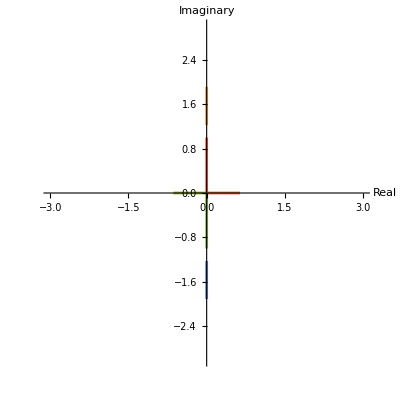
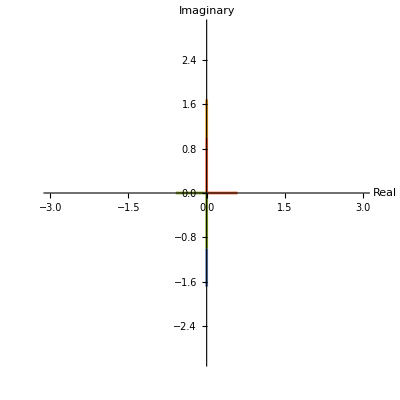
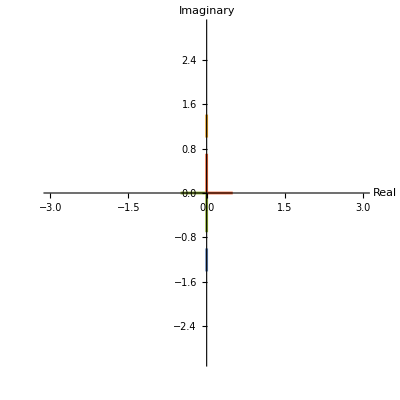

```mathematica
Table[ParametricPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kT->kTman}],Im[eiga[[k]]/.{n->1,kT->kTman}]},{k,1,4}],
{kR,-1,1},
AxesLabel->{"Real","Imaginary"},PlotRange->{-3,3}],
{kTman,-1,1,1/8}]
```

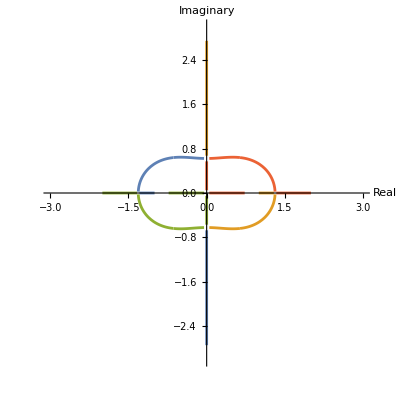
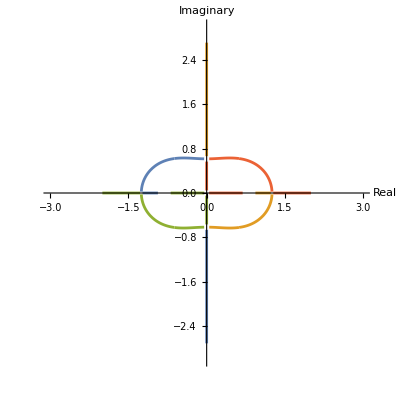
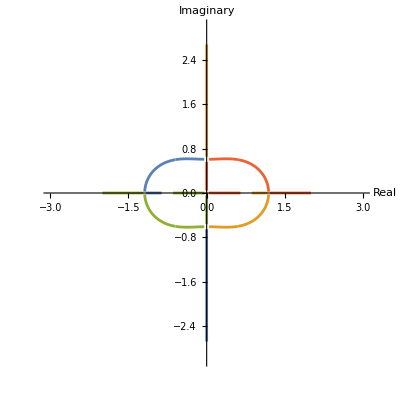
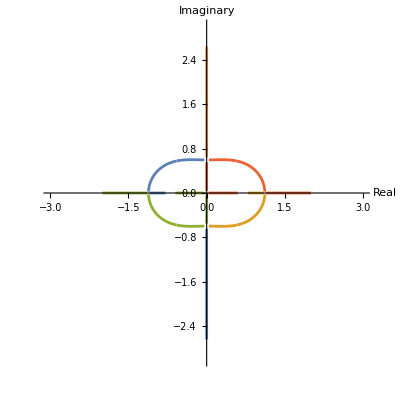
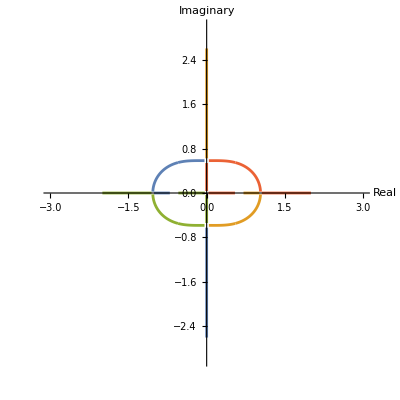
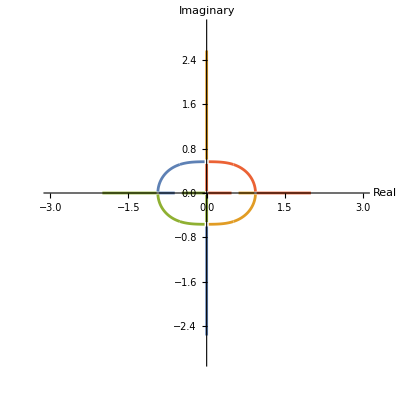
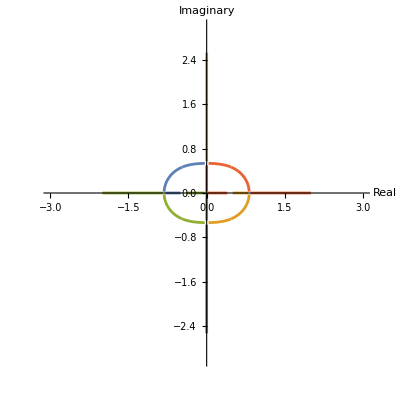
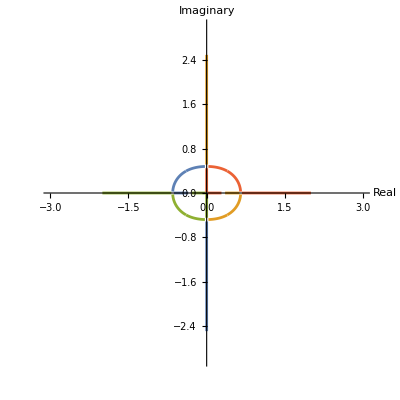

```mathematica
Table[ParametricPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1,kR->kRman}],Im[eiga[[k]]/.{n->1,kR->kRman}]},{k,1,4}],
{kT,-1,1},
AxesLabel->{"Real","Imaginary"},PlotRange->{-3,3}],
{kRman,-1,1,1/8}]
```

```mathematica
ParametricPlot[
Evaluate@Table[{Re[eiga[[k]]/.{n->1}],Im[eiga[[k]]/.{n->1}]},{k,1,4}],
{kR,-1,1},{kT,-1,1},
AxesLabel->{"Real","Imaginary"},FrameStyle->Black,AxesStyle->Black,
BoundaryStyle->Thick,MaxRecursion->5]
```

-Graphics-